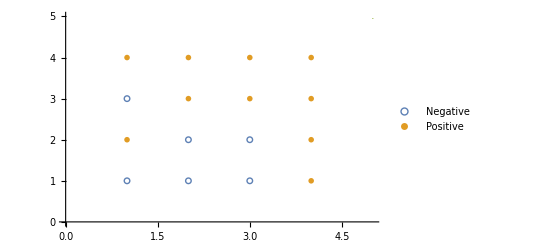

```mathematica
data={{1,1,0},{1,2,1},{1,3,0},{1,4,1},{2,1,0},{2,2,0},{2,3,1},{2,4,1},{3,1,0},{3,2,0},{3,3,1},{3,4,1},{4,1,1},{4,2,1},{4,3,1},{4,4,1}};
positive={};
negative={};
For[a=1,a≤Length[data],If[data[[a]][[3]]==1,positive=Append[positive,data[[a]][[1;;2]]],negative=Append[negative,data[[a]][[1;;2]]]];a+=1]
ListPlot[{negative,positive,{{0,0},{5,5}}},PlotMarkers->{○,X,"."},PlotLegends->{"Negative","Positive"},PlotRange->All]
(*So it means that h(x) is always kept in an abstract form? I think the answer is yes, at least now.*)
h[x_,θ_]:=LogisticSigmoid[Dot[θ,x]];
(*x should always be a vector (n by 1)*)
dataX=data[[All,1;;2]];
dataY=data[[All,3]];
```

```mathematica
(*Use a polynomial of x1 and x2: x1 + x1^2*x2 + x2^2 as the hypothesis. The amount of thetas should be 4, and x1, x2 should be preprocessed into the form of 4 inputs before being applied to the hypothesis*)
```

now epoch 50000, theta is{0.553958, 0.0773482, 0.332574, -3.81726}

now epoch 100000, theta is{0.557543, 0.0770504, 0.333109, -3.82536}

now epoch 150000, theta is{0.557554, 0.0770495, 0.333111, -3.82539}

now epoch 200000, theta is{0.557555, 0.0770495, 0.333111, -3.82539}

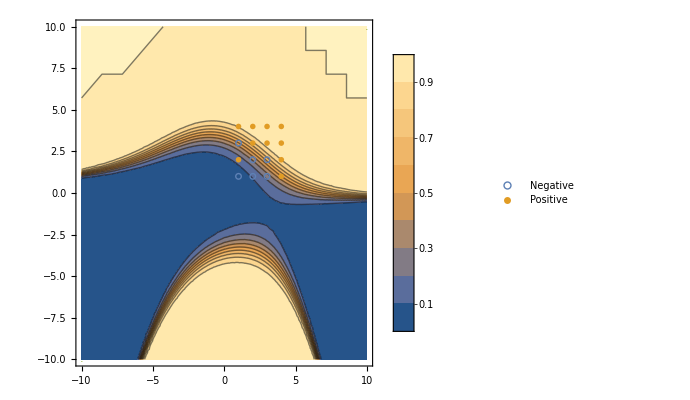

```mathematica
(*Preprocessing xs. Here x should b a vector*)
preprocess[x_]:={x[[All,1]],Power[x[[All,1]],2]*x[[All,2]],Power[x[[All,2]],2],x[[All,1]]*0+1};
dataX1=preprocess[dataX];
θ=dataX1[[All,1]]*0;
α=0.03;
epochs=200000;
(*(batch) gradient descent starts here*)
Do[
(*here the result of h should be a 1-by-n matrix*)
(θ=θ-α*(1/Length[dataX])*Dot[dataX1,h[dataX1,θ]-dataY]);
If[Mod[a,50000]==0,Print["now epoch "<>ToString[a]<>", theta is"<>ToString[θ]]],{a,1,epochs}]
Show[ContourPlot[h[preprocess[{{x,y}}],θ],{x,-10,10},{y,-10,10},PlotLegends->Automatic],ListPlot[{negative,positive,{{-10,-10},{10,10}}},PlotMarkers->{○,X,"."},PlotLegends->{"Negative","Positive"},PlotRange->All]]
```

```mathematica
(*By inputting the calculated thetas above into the following box, you may find that the algorithm has tried its best to distinghuish the two different classes; just choose a favored threshold and the hypothesis can be taken into use. For a better fitting, choose another type of hypothesis.*)
```

```mathematica
Manipulate[Show[ContourPlot[h[preprocess[{{x,y}}],{θ1,θ2,θ3,θ4}],{x,-10,10},{y,-10,10},PlotLegends->Automatic],ListPlot[{negative,positive,{{-10,-10},{10,10}}},PlotMarkers->{○,X,"."},PlotLegends->{"Negative","Positive"},PlotRange->All]],{θ1,-10,10},{θ2,-10,10},{θ3,-10,10},{θ4,-10,10}]
```

```mathematica
(*The hypothesis above may be called "underfitting". Try an overfitting one here*)
```

now epoch 100000, theta is{-8.35984, 21.3078, 15.7073, -16.0622, -16.6102, 4.1587, -2.53557, 1.096, 2.13136, -2.74086}

now epoch 200000, theta is{-11.8993, 29.4091, 22.7743, -20.5344, -22.2467, 5.25408, -3.19502, 0.519555, 2.93784, -5.63643}

now epoch 300000, theta is{-14.0508, 34.4886, 27.2383, -23.2941, -25.949, 5.94353, -3.68599, 0.229729, 3.46923, -7.38983}

now epoch 400000, theta is{-15.6216, 38.1952, 30.497, -25.3085, -28.6534, 6.44763, -4.04786, 0.0218016, 3.85708, -8.67069}

now epoch 500000, theta is{-16.8538, 41.1021, 33.0528, -26.8887, -30.7756, 6.84344, -4.33319, -0.139638, 4.16128, -9.67553}

now epoch 600000, theta is{-17.8655, 43.4886, 35.151, -28.1863, -32.5184, 7.16866, -4.5682, -0.271295, 4.41102, -10.5005}

now epoch 700000, theta is{-18.7227, 45.5104, 36.9286, -29.2859, -33.9953, 7.44434, -4.76773, -0.382308, 4.62261, -11.1994}

now epoch 800000, theta is{-19.4659, 47.2631, 38.4694, -30.2393, -35.2758, 7.68343, -4.94096, -0.478199, 4.80602, -11.8051}

now epoch 900000, theta is{-20.1214, 48.809, 39.8284, -31.0804, -36.4054, 7.89441, -5.09393, -0.562549, 4.9678, -12.3394}

now epoch 1000000, theta is{-20.7076, 50.1915, 41.0436, -31.8327, -37.4156, 8.08313, -5.23083, -0.637811, 5.11248, -12.817}

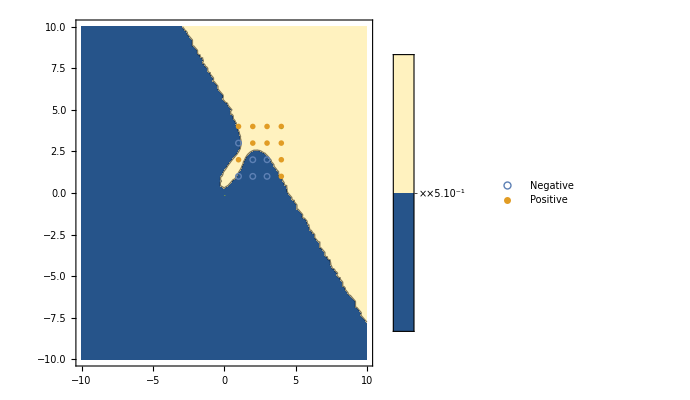

```mathematica
preprocess2[x_]:={x[[All,1]],x[[All,2]],x[[All,1]]*x[[All,2]],Power[x[[All,1]],2],Power[x[[All,2]],2],Power[x[[All,1]],3],Power[x[[All,1]],2]*x[[All,2]],x[[All,1]]*Power[x[[All,2]],2],Power[x[[All,2]],3],x[[All,1]]*0+1};
dataX2=preprocess2[dataX];
θ=dataX2[[All,1]]*0;
α=0.1;
epochs=1000000;
(*(batch) gradient descent starts here*)
Do[
(*here the result of h should be a 1-by-n matrix*)
(θ=θ-α*(1/Length[dataX])*Dot[dataX2,h[dataX2,θ]-dataY]);
If[Mod[a,100000]==0,Print["now epoch "<>ToString[a]<>", theta is"<>ToString[θ]]],{a,1,epochs}]
Show[ContourPlot[h[preprocess2[{{x,y}}],θ],{x,-10,10},{y,-10,10},PlotLegends->Automatic,Contours->{0.5}],ListPlot[{negative,positive,{{0,0},{4,4}}},PlotMarkers->{○,X,"."},PlotLegends->{"Negative","Positive"},PlotRange->All]]
```

```mathematica
(*normalization: though the classification may not do the classification correctly even in its training set, it reduces the abstract value of the parameters, and making the boundary more "general", which is, do not twist the boundary too much for a minority of abnormal data.*)
```

now epoch 100000, theta is{-1.88277, 0.165379, -0.986979, -4.40379, -1.94332, 1.45694, -1.19139, 2.46859, 0.00551576, 4.62111}

now epoch 200000, theta is{-1.92363, 0.105757, -1.04243, -4.42724, -2.01091, 1.56901, -1.22991, 2.39758, 0.0859455, 4.58294}

now epoch 300000, theta is{-1.84257, 0.186479, -0.946761, -4.32437, -1.91001, 1.4372, -1.13968, 2.44559, 0.0811249, 4.62428}

now epoch 400000, theta is{-1.87317, 0.172063, -0.985426, -4.38452, -1.94075, 1.47971, -1.1933, 2.4501, 0.00258775, 4.63377}

now epoch 500000, theta is{-1.82046, 0.131055, -0.939062, -4.21193, -1.96258, 1.47189, -1.14351, 2.41214, 0.206691, 4.59074}

now epoch 600000, theta is{-1.85777, 0.168396, -0.970984, -4.34566, -1.9183, 1.39692, -1.20818, 2.4334, 0.116107, 4.61683}

now epoch 700000, theta is{-1.82003, 0.214973, -0.924191, -4.2783, -1.81266, 1.50385, -1.16143, 2.50979, 0.392316, 4.64443}

now epoch 800000, theta is{-1.87182, 0.168169, -0.973737, -4.38069, -1.94907, 1.45146, -1.13664, 2.44424, -0.00411507, 4.63529}

now epoch 900000, theta is{-1.94496, 0.111025, -1.08887, -4.45649, -1.94068, 1.44475, -1.39284, 2.29557, 0.294088, 4.53028}

now epoch 1000000, theta is{-1.93893, 0.1346, -1.0342, -4.4591, -1.939, 1.49918, -1.15816, 2.48707, 0.117718, 4.58309}

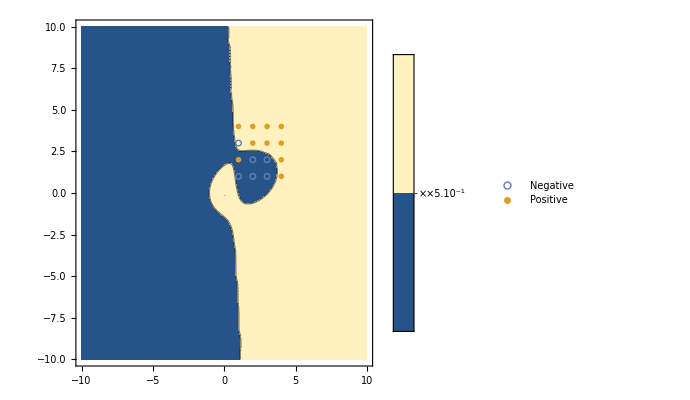

```mathematica
θ=dataX2[[All,1]]*0;
α=0.1;
λ=1.;
m=Length[dataX];
epochs=1000000;
mask=IdentityMatrix[Length[θ]]*1;
mask[[-1,-1]]=0;
(*(batch) gradient descent starts here*)
Do[
(*here the result of h should be a 1-by-n matrix*)
θ=θ-α/m*(Dot[dataX2,h[dataX2,θ]-dataY]+λ/m*Dot[θ,mask]);
If[Mod[a,100000]==0,Print["now epoch "<>ToString[a]<>", theta is"<>ToString[θ]]],{a,1,epochs}]
Show[ContourPlot[h[preprocess2[{{x,y}}],θ],{x,-10,10},{y,-10,10},PlotLegends->Automatic,Contours->{0.5}],ListPlot[{negative,positive,{{0,0},{4,4}}},PlotMarkers->{○,X,"."},PlotLegends->{"Negative","Positive"},PlotRange->All]]
```